```mathematica
Quit[]
Remove["*"]
```

```mathematica
FindLibrary["libcollierX"]
Needs["CollierLink`"]
Needs["X`"]
Print[$Packages]
```

/home/kds/.Mathematica/Applications/CollierLink/LibraryResources/Linux-x86-64/libcollierX.so

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

CollierLink v1.0.1, by Hiren H. Patel
For more information, see the

{Parallel`Protected`,Parallel`Developer`,Parallel`Evaluate`,GeneralUtilities`,Templating`,Parallel`Combine`,Parallel`Queue`Priority`,Parallel`Queue`FIFO`,Parallel`Queue`Interface`,Parallel`Concurrency`,Parallel`VirtualShared`,Parallel`Status`,RemoteEvaluators`WSTPServerKernels`,RemoteEvaluators`SshKernels`,RemoteEvaluators`SelfKernels`,RemoteEvaluators`LocalKernels`,RemoteEvaluators`CloudKernels`,RemoteKernelObject`,SubKernels`RemoteKernelBridge`,Parallel`Palette`,Parallel`Parallel`,SubKernels`Protected`,SubKernels`,Parallel`Kernels`,Parallel`,Parallel`Debug`Perfmon`,Parallel`Debug`,Parallel`Preferences`,X`,CollierLink`,DocumentationSearch`,ProcessLink`,ErrorHandling`,EntityFramework`WolframAlphaEntityStore`,EntityFramework`Utilities`,EntityFramework`ToFromEntity`,EntityFramework`SideEffects`,EntityFramework`Registry`,EntityFramework`Preferences`,EntityFramework`Predicates`,EntityFramework`OperatorForms`,EntityFramework`Ontology`,EntityFramework`InterpreterCache`,EntityFramework`Formatting`,EntityFramework`Filter`,EntityFramework`FileKeyValueStore`,EntityFramework`FileAssociation`,EntityFramework`EvaluateWrapper`,EntityFramework`EvaluateQualified`,EntityFramework`EvaluateExists`,EntityFramework`EvaluateEntity`,EntityFramework`EvaluateComplexEntity`,EntityFramework`EntityValue`,EntityFramework`EntityTypeObject`,EntityFramework`EntityTypeList`,EntityFramework`EntityType`,EntityFramework`EntityStoreFeatures`,EntityFramework`EntityStore`,EntityFramework`EntityProperties`,EntityFramework`EntityPrefetch`,EntityFramework`EntityMetaInformation`,EntityFramework`EntityList`,EntityFramework`EntityInstance`,EntityFramework`EntityFunctions`,EntityFramework`EntityFunction`,EntityFramework`DisambiguateEntityProperty`,EntityFramework`DefaultEntityTypes`,EntityFramework`DataUtilities`,EntityFramework`DataFunctions`,EntityFramework`CustomEntity`,EntityFramework`ComputedProperties`,EntityFramework`CommonName`,EntityFramework`Caching`,EntityFramework`BatchMap`,EntityFramework`BatchDownload`,EntityFramework`BatchApplied`,EntityFramework`AsynchronousPrefetch`,EntityFramework`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,GetFEKernelInit`,RemoteEvaluate`,URLUtilities`,KeychainLink`,UnitTable`,QuestionFramework`,CloudObject`CreateUUID`,CloudObjectLoader`,ResourceFunctionHelpers`,CloudDialogs`,CSGRegion`Load`,Regions`Load`,NurbsRegion`Load`,ImportExport`Load`,WebAudioSearchLoader`,NeuralNetworks`,NeuralFunctions`,NaturalLanguageProcessingLoader`,NaturalLanguage`,MobileMessaging`,Interpreter`,IntegratedServices`,IconizeLoader`,HTTPHandling`,GeoTools`,GeometrySearchLoader`,Forms`,FormNotebook`,ExternalEvaluate`,DatasetLoader`,Cryptography`,CloudExpressionLoader`,Blockchain`,Authentication`,SystemTools`,SecureShellLink`,MailLink`,IMAPLink`,ExternalStorage`,PacletManager`,WolframAppCatalog`,ResourceLocator`,PersistenceLocations`,System`,Global`}

```mathematica
Print["Trying:"]
d = 4;
B0[1000,10,10]
C0i[cc0,0.1,0.1,1,0.1,0.100,0.200]
TraditionalForm[PVC[1,1,0,a,b,c,d,e,f]]
TraditionalForm[PVC[0,1,0,a,b,c,d,e,f]]
```

Trying:

B0[1000,10,10]

C0i[cc0,0.1,0.1,1,0.1,0.1,0.2]

C_(0,0,1)(a,b,c;4,e,f)

C_1(a,b,c;4,e,f)

```mathematica
m = 10^(-3);
mZ=91.187*m;
m1=125*m;
m2=500*m;
v=246.22*m;
m3=(v^2+m2^2)^(0.5);

LT[q_,mi_,mj_,mk_]:=-C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mj^2,mk^2]+C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mj^2,mZ^2]+C0i[cc001,q^2,mZ^2,mZ^2,mZ^2,mj^2,mk^2]+C0i[cc001,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]-mZ^2 C0i[cc1,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2];
CPLT[q_,mi_,mj_,mk_]:=LT[q,mi,mj,mk]-LT[q,mi,mk,mj]-LT[q,mj,mi,mk]+LT[q,mj,mk,mi]+LT[q,mk,mi,mj]-LT[q,mk,mj,mi];

CP[q_,mi_,mj_,mk_]:=-PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mZ^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mj^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]-mZ^2 PVC[0,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2];
PV[q_,mi_,mj_,mk_]:=CP[q,mi,mj,mk]-CP[q,mi,mk,mj]-CP[q,mj,mi,mk]+CP[q,mj,mk,mi]+CP[q,mk,mi,mj]-CP[q,mk,mj,mi];
CP1[q_,mi_,mj_,mk_]:=
-PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mk^2,mi^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mi^2,mj^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mk^2,mj^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mj^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mi^2,mk^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mj^2,mZ^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mk^2,mZ^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mi^2,mZ^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mi^2,mZ^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mk^2,mZ^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mj^2,mZ^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mj^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mi^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mk^2,mj^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mi^2,mj^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mj^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mZ^2,mk^2,mi^2]+
PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mi^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]+PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mj^2]-
PVC[1,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mj^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mk^2]-PVC[1,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mi^2]-
mZ^2(PVC[0,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mi^2]+PVC[0,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mk^2]+PVC[0,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mj^2]-
PVC[0,1,0,q^2,mZ^2,mZ^2,mi^2,mZ^2,mj^2]-PVC[0,1,0,q^2,mZ^2,mZ^2,mj^2,mZ^2,mk^2]-PVC[0,1,0,q^2,mZ^2,mZ^2,mk^2,mZ^2,mi^2]);
Delt[q_,mi_,mj_,mk_]:=PV[q,mi,mj,mk]-CPLT[q,mi,mj,mk];

Abs[PV[2,m1,m2,m3]]
Abs[PV[2/m,m1/m,m2/m,m3/m]]

Abs[CPLT[2/m,m1/m,m2/m,m3/m]]
Abs[CPLT[2,m1,m2,m3]]
Print["----"]
N[PVC[0,1,0,1^2,1^2,2^2,1^2,2^2,3^2]]
N[PVC[0,1,0,1000^2,1000^2,2000^2,1000^2,2000^2,3000^2]]
Print["----"]
N[C0i[cc1,2^2,mZ^2,mZ^2,m1^2,m2^2,m3^2]]
N[C0i[cc1,2000^2,(mZ/m)^2,(mZ/m)^2,(m1/m)^2,(m2/m)^2,(m3/m)^2]]
(*Они зависят от масштаба*)
```

0.000225988

4.15594×10^-7

Abs[C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,15625,250000]-C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,15625,310624.]-C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,250000,15625]+C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,250000,310624.]+C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,310624.,15625]-C0i[cc001,4000000,0.00831507,0.00831507,0.00831507,310624.,250000]-C0i[cc001,4000000,0.00831507,0.00831507,15625,0.00831507,250000]+C0i[cc001,4000000,0.00831507,0.00831507,15625,0.00831507,310624.]+C0i[cc001,4000000,0.00831507,0.00831507,15625,250000,0.00831507]-C0i[cc001,4000000,0.00831507,0.00831507,15625,250000,310624.]-C0i[cc001,4000000,0.00831507,0.00831507,15625,310624.,0.00831507]+C0i[cc001,4000000,0.00831507,0.00831507,15625,310624.,250000]+C0i[cc001,4000000,0.00831507,0.00831507,250000,0.00831507,15625]-C0i[cc001,4000000,0.00831507,0.00831507,250000,0.00831507,310624.]-C0i[cc001,4000000,0.00831507,0.00831507,250000,15625,0.00831507]+C0i[cc001,4000000,0.00831507,0.00831507,250000,15625,310624.]+C0i[cc001,4000000,0.00831507,0.00831507,250000,310624.,0.00831507]-C0i[cc001,4000000,0.00831507,0.00831507,250000,310624.,15625]-C0i[cc001,4000000,0.00831507,0.00831507,310624.,0.00831507,15625]+C0i[cc001,4000000,0.00831507,0.00831507,310624.,0.00831507,250000]+C0i[cc001,4000000,0.00831507,0.00831507,310624.,15625,0.00831507]-C0i[cc001,4000000,0.00831507,0.00831507,310624.,15625,250000]-C0i[cc001,4000000,0.00831507,0.00831507,310624.,250000,0.00831507]+C0i[cc001,4000000,0.00831507,0.00831507,310624.,250000,15625]+0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,15625,0.00831507,250000]-0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,15625,0.00831507,310624.]-0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,250000,0.00831507,15625]+0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,250000,0.00831507,310624.]+0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,310624.,0.00831507,15625]-0.00831507 C0i[cc1,4000000,0.00831507,0.00831507,310624.,0.00831507,250000]]

Abs[C0i[cc001,4,0.00831507,0.00831507,0.00831507,1/64,1/4]-C0i[cc001,4,0.00831507,0.00831507,0.00831507,1/64,0.310624]-C0i[cc001,4,0.00831507,0.00831507,0.00831507,1/4,1/64]+C0i[cc001,4,0.00831507,0.00831507,0.00831507,1/4,0.310624]+C0i[cc001,4,0.00831507,0.00831507,0.00831507,0.310624,1/64]-C0i[cc001,4,0.00831507,0.00831507,0.00831507,0.310624,1/4]-C0i[cc001,4,0.00831507,0.00831507,1/64,0.00831507,1/4]+C0i[cc001,4,0.00831507,0.00831507,1/64,0.00831507,0.310624]+C0i[cc001,4,0.00831507,0.00831507,1/64,1/4,0.00831507]-C0i[cc001,4,0.00831507,0.00831507,1/64,1/4,0.310624]-C0i[cc001,4,0.00831507,0.00831507,1/64,0.310624,0.00831507]+C0i[cc001,4,0.00831507,0.00831507,1/64,0.310624,1/4]+C0i[cc001,4,0.00831507,0.00831507,1/4,0.00831507,1/64]-C0i[cc001,4,0.00831507,0.00831507,1/4,0.00831507,0.310624]-C0i[cc001,4,0.00831507,0.00831507,1/4,1/64,0.00831507]+C0i[cc001,4,0.00831507,0.00831507,1/4,1/64,0.310624]+C0i[cc001,4,0.00831507,0.00831507,1/4,0.310624,0.00831507]-C0i[cc001,4,0.00831507,0.00831507,1/4,0.310624,1/64]-C0i[cc001,4,0.00831507,0.00831507,0.310624,0.00831507,1/64]+C0i[cc001,4,0.00831507,0.00831507,0.310624,0.00831507,1/4]+C0i[cc001,4,0.00831507,0.00831507,0.310624,1/64,0.00831507]-C0i[cc001,4,0.00831507,0.00831507,0.310624,1/64,1/4]-C0i[cc001,4,0.00831507,0.00831507,0.310624,1/4,0.00831507]+C0i[cc001,4,0.00831507,0.00831507,0.310624,1/4,1/64]+0.00831507 C0i[cc1,4,0.00831507,0.00831507,1/64,0.00831507,1/4]-0.00831507 C0i[cc1,4,0.00831507,0.00831507,1/64,0.00831507,0.310624]-0.00831507 C0i[cc1,4,0.00831507,0.00831507,1/4,0.00831507,1/64]+0.00831507 C0i[cc1,4,0.00831507,0.00831507,1/4,0.00831507,0.310624]+0.00831507 C0i[cc1,4,0.00831507,0.00831507,0.310624,0.00831507,1/64]-0.00831507 C0i[cc1,4,0.00831507,0.00831507,0.310624,0.00831507,1/4]]

----

0.0077682+0. ⅈ

7.61305×10^-15+0. ⅈ

----

C0i[cc1,4.,0.00831507,0.00831507,0.015625,0.25,0.310624]

C0i[cc1,4.×10^6,8315.07,8315.07,15625.,250000.,310624.]

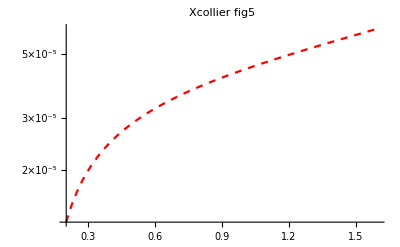

-Graphics-

-Graphics-

-Graphics-

```mathematica
b= 2;
p0=LogPlot[Abs[PV[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotStyle->{Red,Dashed},PlotLabel->"Xcollier fig5"];
p3=LogPlot[Abs[CPLT[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotLabel->"LoopTools fig5"];
Show[p0,p3]
P = LogPlot[Abs[PV[x,m1,b,√((b)^2+v^2)]]-Abs[CPLT[x,m1,b,√((b)^2+v^2)]],{x,0.200,1.60},PlotLabel->"LoopTools vs Xcollier"]
p1 = LogLogPlot[Re[CPLT[1.000,m1,x,√((x)^2+v^2)]], {x, 0.100, 10.000},PlotLabel->"LoopTools Re fig7"]
p2 = LogLogPlot[Im[CPLT[1.000,m1,x,√((x)^2+v^2)]], {x, 0.100, 10.000},PlotLabel->"LoopTools Im fig7"]
```